# Cuestionario_03: Ecuaciones.

Sea

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);     h[x_]:=Sin[x/3] - Cos[x^3/5]
```

1. Encuentra las tres soluciones exactas de  f(x)=0.

```mathematica
Solve[f[x]==0]
```

{{x→1},{x→2-√5},{x→2+√5}}

otra forma

```mathematica
Solve[(x^3-5 x^2+3x+1)/(2 x^2+x-1)==0]
```

{{x→1},{x→2-√5},{x→2+√5}}

```mathematica
N[%]
```

{{x→1.},{x→-0.236068},{x→4.23607}}

Las tres soluciones ordenadas de menor a mayor son:
x_1=  2-√5   ,x_2=    1        ,x_3=     2+√5

2 .Encuentra  x ∈ ℝ tal que  f(x) ≥0

```mathematica
Reduce[(x^3-5 x^2+3x+1)/(2 x^2+x-1)≥0,x]
```

-1<x≤2-√5||1/2<x≤1||x≥2+√5

Otra forma mucho más larga  de resolver el mismo ejercicio:

```mathematica
Solve[2 x^2+x-1==0]
```

{{x→-1},{x→1/2}}

Los puntos donde la función puede cambiar de signo son {{x→1},{x→2-√5},{x→2+√5}} y {{x→-1},{x→1/2}} . Podemos ordenarlos en orden creciente para ver los intervalos en la recta real{x→-1},{x→2-√5},{x→1/2},{x→1},x→2+√5}, así

```mathematica
(x^3-5 x^2+3x+1)/(2 x^2+x-1)/. x->{-500,-0.8,0,0.75,0.3,500}
```

{-11477409/45409,9.83077,-1,0.982143,-2.84038,123751501/500499}

La solución es:
]  -1    , 2-√5    ]     ∪     ]  1/2      ,1  ]   ∪     [  2+√5      ,+∞[

además podeis verificar la solución anterior usando Plot[]

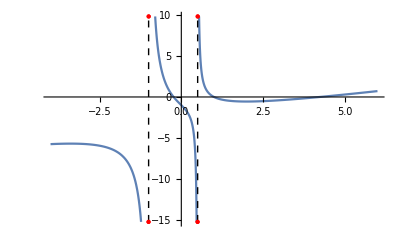

```mathematica
Plot[(x^3-5 x^2+3x+1)/(2 x^2+x-1),{x,-4,6},ExclusionsStyle->{Dashing[Small],Red}]
```

3 .Obtén el valor aproximado donde la función  h(x) alcanza su mínimo local cerca de  x=3

```mathematica
D[Sin[x/3] - Cos[x^3/5],x]
```

1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]

Solve y NSolve no nos van a dar una solución

```mathematica
Solve[%==0,x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]

```mathematica
NSolve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]

Por eso tenemos que usar FindRoot

```mathematica
FindRoot[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5], {x, 3.}]
```

{x→3.1507}

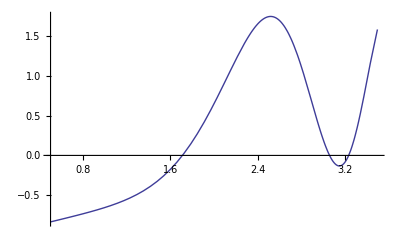

```mathematica
Plot[Sin[x/3] - Cos[x^3/5],{x,0.5,3.5}]
```

x≈3.1507

puedes utilizar la función  mouse position para comprobar la solución

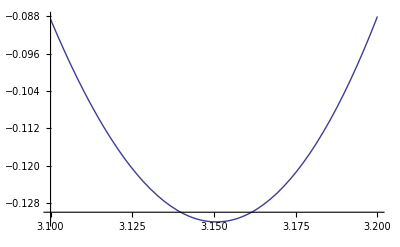

```mathematica
AA=Plot[Sin[x/3] - Cos[x^3/5],{x,3.1,3.2}]
```

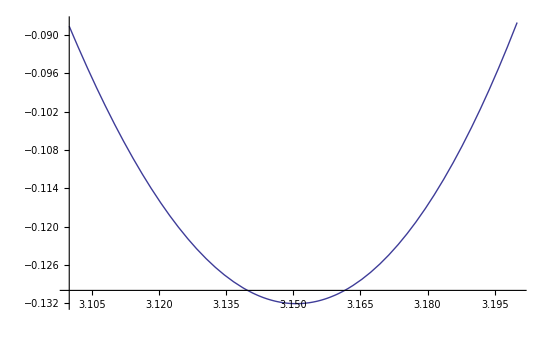

```mathematica
{Graphics[AA,ImageSize->100],Dynamic[MousePosition["Graphics","Mouse not in graphics!"]]}
```